-Graphics3D-

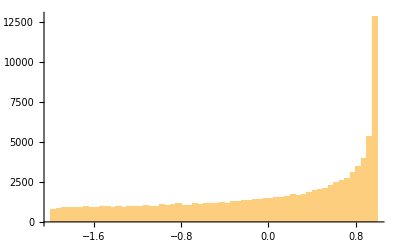

-0.00421399

```mathematica
makeRotationMatrix[num_]:=Table[Orthogonalize[RandomVariate[NormalDistribution[],{3,3}]],num];
rotations=makeRotationMatrix[100000];

B0vector={0,0,1.};
ListPointPlot3D[#.B0vector&/@rotations,BoxRatios->1]

makeDDTensor[vec_]:=-(3KroneckerProduct[vec,vec]-vec.vec IdentityMatrix[3]);
DDTensors=makeDDTensor[#]&/@(#.B0vector&/@rotations);
DDCoupling=B0vector.#.B0vector&/@DDTensors;

Histogram[DDCoupling,50]
Mean@DDCoupling
```